# HW 2 - ASTR540

## Daniel George - dgeorge5@illinois.edu

## Q1)

## a)

Let R be the radius of the Sun and d be the distance from the earth to the Sun, then:

```mathematica
eqΩ=Ω == Pi R^2/d^2
```

Ω==(π R^2)/d^2

Let FR be the flux at the surface of the sun, then flux at distance r from the Sun is given by:

```mathematica
F[r_]=FR R^2/r^2
```

(FR R^2)/r^2

Flux at earth (Fd) is:

```mathematica
eqFd=Fd==F[d]
```

Fd==(FR R^2)/d^2

Solving for FR and substituting the value of R in terms of Ω:

```mathematica
sFRd=Solve[eqFd,FR][[1,1]]/.Solve[eqΩ,R][[1]]
```

FR→(Fd π)/Ω

## b)

Given angular diameter to be .57°:

```mathematica
eqA=2 R/d == .57°
```

(2 R)/d==0.00994838

Solid angle subtended by sun:

```mathematica
sΩ=Ω->Last[eqΩ/.Solve[eqA,R][[1]]]
```

Ω→0.000077731

## c)

Substituting the value of flux at Earth:

```mathematica
sFR=sFRd/.Fd->Quantity[1.4, ("Kilowatts")/("Meters")^2]/.sΩ
```

FR→56582.7 kW/m^2

Using Stefan-Boltzmann law and solving for T:

```mathematica
Solve["T" "Temperature">0&&FR==(Quantity[1, "StefanBoltzmannConstant"]) ("T" "Temperature")^4/.sFR,"T" "Temperature"]
```

{{T Temperature→5620.41 K}}

## d)

We have the following formula:

```mathematica
Equal@@sFRd
```

FR==(Fd π)/Ω

Flux at the surface of Sun is given by:

```mathematica
sF=FR->Pi FormulaData[{"PlanckRadiationLaw", "Wavelength"}][[2]]
```

FR→(2 π h c^2)/((-1+ⅇ^((1 h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)

Substituting above:

```mathematica
eqT=Equal@@sFRd/.sF
```

(2 π h c^2)/((-1+ⅇ^((1 h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)==(Fd π)/Ω

Therefore we can solve the above equation for temperature.

## Q3)

Defining number density (nd):

```mathematica
nd=Quantity[0.1, 1/("Parsecs")^3];
```

Finding maximum distance (d):

```mathematica
sd=NSolve[Quantity[0.01, "ArcSeconds"]==1 Quantity[, "AstronomicalUnit"]/d,d][[1,1]]
```

d→2.06265×10^7 au

Number of stars in sphere of radius d:

```mathematica
nd 4/3Pi d^3/.sd
```

418879.

## Q4)

## e)

Defining function to find ratio of specific intensities:

```mathematica
iRatio[τ_,b_]:=(1-Exp[-τ Sqrt[1-b^2]])/(1-Exp[-τ])
```

Plotting ratio vs b for different τ:

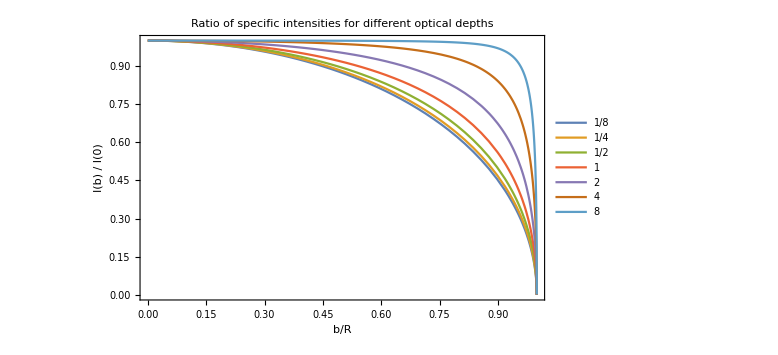

```mathematica
With[{list={1/8,1/4,1/2,1,2,4,8}},Plot[Evaluate@Table[iRatio[τ,b],{τ,list}],{b,0,1},Frame->True,PlotRange->All,PlotLegends->Placed[list,{Left,Center}],FrameLabel->{"b/R","I(b) / I(0)"},PlotLabel->"Ratio of specific intensities for different optical depths",ImageSize->Large]]
```